```mathematica
ClearAll["Global`*"]
u={u1,u2}
L={{-5,1},{5,-1}};
λ=Eigenvalues[L]
Norm[L]
2.5/Norm[L]
T=Eigenvectors[L];
FindInstance[u.L.u>0&&u1≥0&&u2≥0&&u1+u2==1,u]
Reduce[u.L.u≤0,u]
```

{u1,u2}

{-6,0}

2 √13

0.346688

{{u1→1/4,u2→3/4}}

u2∈ℝ&&((u1<0&&(u2≤5 u1||u2≥u1))||u1==0||(u1>0&&(u2≤u1||u2≥5 u1)))

{-1/9,10/9}

{-5,5}

{5,-5}

{-5,5}

{5,-5}

1/45≤α≤2/9

{{dt→Root0.309Root[-1+5 #1-15 #1^2+30 #1^3&,1]0.30948645711516276}}

{{dt→Root0.309Root[-1+5 #1-15 #1^2+30 #1^3&,1]0.30948645711516276}}

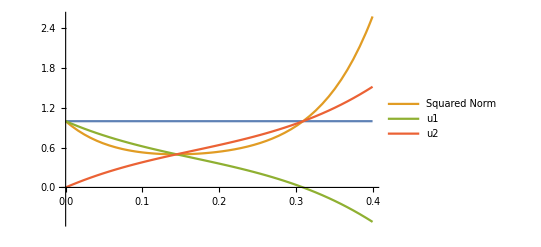

```mathematica
ClearAll["Global`*"]
L={{-5,1},{5,-1}};
u0={1,0};
y1=u0;
y2=u0+dt*L.y1;
y3=u0+1/4*dt*L.y1+1/4*dt*L.y2;
u1=Simplify[u0+1/6*dt*L.y1+1/6*dt*L.y2+2/3*dt*L.y3];

dtChosen=1/3;
u1Chosen=Simplify[u1/.{dt->dtChosen}]
Simplify[L.y1/.{dt->dtChosen}]
Simplify[L.y2/.{dt->dtChosen}]
Simplify[L.y3/.{dt->dtChosen}]
alphaVector=Simplify[(1/2*L.y1+1/2*L.y2-L.y3)/.{dt->dtChosen}]
Reduce[(u1Chosen+α*alphaVector)[[1]]≥0&&(u1Chosen+α*alphaVector)[[2]]≥0,α]

Solve[u1[[1]]^2+u1[[2]]^2==u0[[1]]^2+u0[[2]]^2&&dt>0,dt]
Solve[Min[u1[[1]],u1[[2]]]==0&&dt>0,dt]
Plot[{u0[[1]]^2+u0[[2]]^2,Legended[u1[[1]]^2+u1[[2]]^2,"Squared Norm"],Legended[u1[[1]],"u1"],Legended[u1[[2]],"u2"]},{dt,0,0.4}]
```